## Probabilità dal minimo

```mathematica
L=80;
hx=0.8;
hz=0.02;
δt=15;
chain={Table[-1,{i,1,L}]};
chainplus=Table[-1,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^((min[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

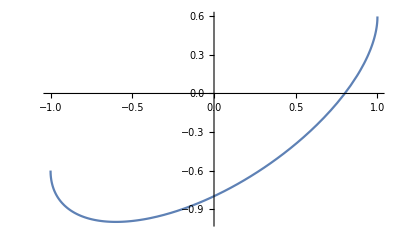

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

Piecewise[{{1.98196 ⅇ^(15 (-1.-0.6 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

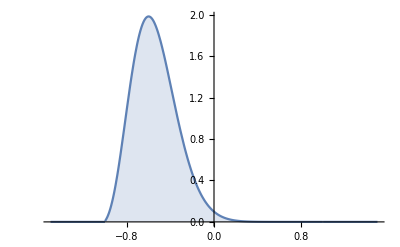

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.823531

```mathematica
chain={Table[-1,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,10}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
chain
```

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

```mathematica
0.02
```

-Graphics-

```mathematica
0.03
```

-Graphics-

```mathematica
0.01
```

-Graphics-

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

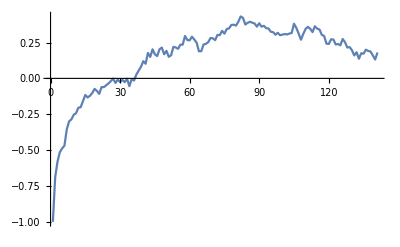

```mathematica
0.02
```

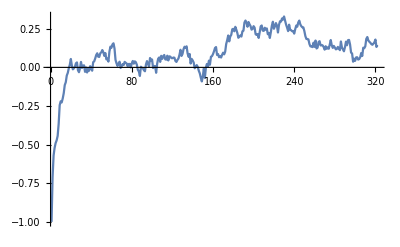

```mathematica
0.01
```

```mathematica
hz=0.05
```

-Graphics-

```mathematica
hz=0.05
```

-Graphics-

```mathematica
hz=0.1
```

-Graphics-

```mathematica
hz=0.4
```

-Graphics-

```mathematica
hz=0.2
```

-Graphics-

```mathematica
hz=0.4
```

-Graphics-

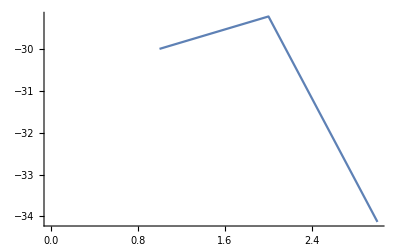

```mathematica
ListLinePlot[energ]
```

Piecewise[{{0.747597 ⅇ^(-1.13715+0.808157 zi+0.8 √(1-zi^2)), -1<zi<1}, {0, True}}]

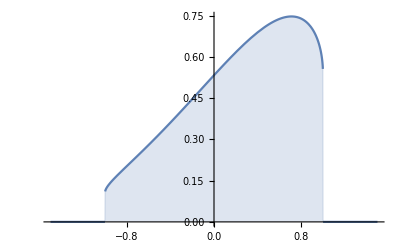

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

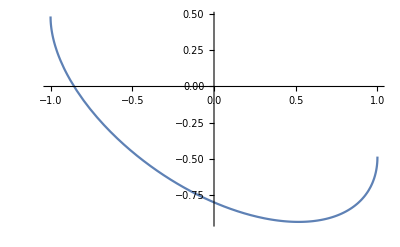

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

## Probabilità dallo stato attuale

```mathematica
L=80;
hx=0.8;
hz=0.01;
δt=30;
chain={Table[-1,{i,1,L}]};
chainplus=Table[-1,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

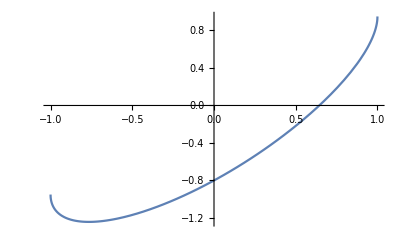

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

Piecewise[{{0.000599648 ⅇ^(30 (-0.95-0.95 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

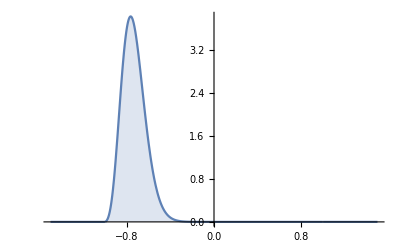

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.823531

```mathematica
chain={Table[-1,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,10}]
```

Interpolation::inddp: The point -2.6487×10^-8 in dimension 1 is duplicated.

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

```mathematica
0.01 30
```

-Graphics-

```mathematica
0.02 30
```

-Graphics-

```mathematica
0.05 30
```

-Graphics-

```mathematica
0.01 15
```

-Graphics-

```mathematica
0.05
```

-Graphics-

```mathematica
0.1
```

-Graphics-

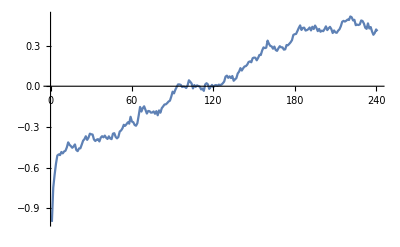

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

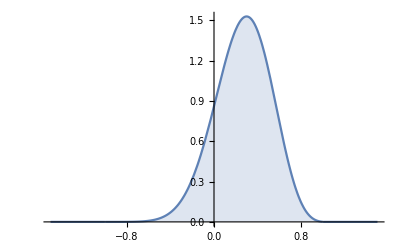

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

## Probabilità dallo stato attuale alternativa

```mathematica
L=80;
hx=0.8;
hz=0.01;
δt=80;
chain={Table[-1,{i,1,L}]};
chainplus=Table[-1,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[1/(1+ⅇ^((energyi[i]-energy[i])δt)),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

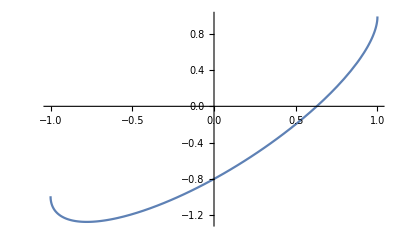

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

Piecewise[{{1.2667/(1+ⅇ^(80 (0.99+0.99 zi-0.8 √(1-zi^2)))), -1<zi<1}, {0, True}}]

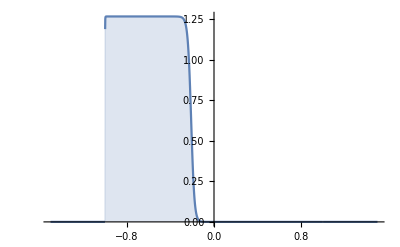

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.823531

```mathematica
chain={Table[-1,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,50}]
```

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

```mathematica
0.01
```

-Graphics-

```mathematica
0.02
```

-Graphics-

```mathematica
0.05
```

-Graphics-

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

-Graphics-

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

```mathematica
chain={Table[-1,{i,1,L}]};
```

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

Piecewise[{{1.2667/(1+ⅇ^(80 (0.99+0.99 zi-0.8 √(1-zi^2)))), -1<zi<1}, {0, True}}]

-Graphics-

## Probabilità dallo stato attuale simmetria Z2

```mathematica
L=80;
hx=0.8;
hz=0.;
δt=250;
chain={Table[0,{i,1,L}]};
chainplus=Table[0,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

-Graphics-

Piecewise[{{5.65251 ⅇ^(250 (-0.8+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

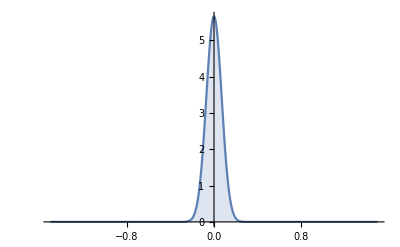

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.823531

```mathematica
chain={Table[0,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,500}]
```

Interpolation::inddp: The point 5.3666×10^-8 in dimension 1 is duplicated.

Interpolation::inddp: The point -5.89563×10^-8 in dimension 1 is duplicated.

Interpolation::inddp: The point 2.45399×10^-8 in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

-Graphics-

```mathematica
last=chain[[Length[chain]]]
```

{-0.61022,0.580718,-0.616115,0.53373,-0.594599,0.615362,-0.512105,0.381113,-0.587088,-0.323097,-0.559011,-0.564798,-0.511213,-0.484555,-0.652871,-0.687802,-0.629281,-0.590948,-0.670677,-0.598963,-0.537326,-0.662409,-0.561519,-0.658145,-0.492047,-0.569077,-0.68427,-0.451725,-0.663991,-0.499056,-0.632777,-0.599227,-0.571478,-0.483326,-0.517363,-0.544923,-0.4438,-0.614314,-0.0663107,-0.573355,0.147928,-0.555334,0.597176,-0.565079,0.662564,-0.493907,0.617448,-0.568111,0.686385,-0.640047,0.582018,-0.670343,0.580321,-0.623418,0.598196,-0.565179,0.58464,-0.45669,0.616389,0.122196,0.614026,0.431733,0.72431,0.660317,0.59592,0.539518,0.658405,0.629593,0.477018,0.636603,0.561784,0.461688,0.395273,0.548905,-0.0853923,0.538216,-0.400716,0.617704,-0.50707,0.555292}

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

## Probabilità dallo stato attuale simmetria Z2 two-turns

```mathematica
L=180;
hx=0.8;
hz=0.;
δt=250;
chain={Table[0,{i,1,L}]};
chainplus=Table[0,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

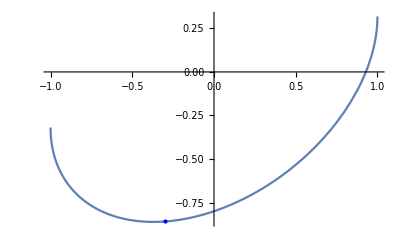

```mathematica
n=9;
Plot[energyi[n],{zi,-1,1},Epilog->{Blue,PointSize@Large,Point[{chain[[Length[chain],n]],energy[n]}]}]
```

```mathematica
chain[[Length[chain],9]]
```

-0.301102

Piecewise[{{3.53846 ⅇ^(250 (-0.858859-0.31878 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

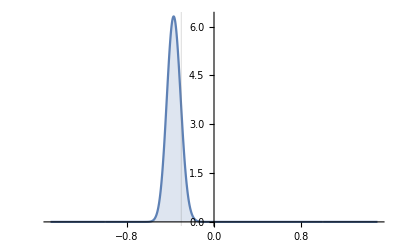

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},GridLines->{{{chain[[Length[chain],9]],{Red,Dashed,Thick}}},None},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.823531

```mathematica
chain={Table[0,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[If[(EvenQ[Length[chain]]&&EvenQ[i])||(OddQ[Length[chain]]&&OddQ[i]),RandomVariate[𝒟[i]],chain[[Length[chain],i]]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,50}]
```

Interpolation::inddp: The point 1.43617×10^-8 in dimension 1 is duplicated.

Interpolation::inddp: The point 2.16863×10^-9 in dimension 1 is duplicated.

Interpolation::inddp: The point 1.04576×10^-8 in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

```mathematica
.
```

-Graphics-

```mathematica
.
```

-Graphics-

```mathematica
last=chain[[Length[chain]]]
```

{-0.61022,0.580718,-0.616115,0.53373,-0.594599,0.615362,-0.512105,0.381113,-0.587088,-0.323097,-0.559011,-0.564798,-0.511213,-0.484555,-0.652871,-0.687802,-0.629281,-0.590948,-0.670677,-0.598963,-0.537326,-0.662409,-0.561519,-0.658145,-0.492047,-0.569077,-0.68427,-0.451725,-0.663991,-0.499056,-0.632777,-0.599227,-0.571478,-0.483326,-0.517363,-0.544923,-0.4438,-0.614314,-0.0663107,-0.573355,0.147928,-0.555334,0.597176,-0.565079,0.662564,-0.493907,0.617448,-0.568111,0.686385,-0.640047,0.582018,-0.670343,0.580321,-0.623418,0.598196,-0.565179,0.58464,-0.45669,0.616389,0.122196,0.614026,0.431733,0.72431,0.660317,0.59592,0.539518,0.658405,0.629593,0.477018,0.636603,0.561784,0.461688,0.395273,0.548905,-0.0853923,0.538216,-0.400716,0.617704,-0.50707,0.555292}

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

```mathematica
chain[[Length[chain],9]]
```

## Probabilità dallo stato attuale simmetria Z2 distance

```mathematica
L=180;
hx=0.8;
hz=0.;
δt=5;
δs=5;
chain={Table[0,{i,1,L}]};
chainplus=Table[0,{i,1,L}];
```

```mathematica
chain={{-0.6102201217525546,0.5807184769885196,-0.6161154938350316,0.5337302094209458,-0.5945986980737,0.6153621569073828,-0.5121045825660978,0.3811134527038774,-0.5870882694997746,-0.3230965846393222,-0.5590106394825953,-0.564797911262122,-0.5112132695624015,-0.48455521009750646,-0.6528710012476006,-0.6878021506276948,-0.6292805453868601,-0.5909483280122911,-0.6706765437895488,-0.5989630914430591,-0.537326494381948,-0.6624091865907064,-0.5615191547581165,-0.6581452402256573,-0.4920465057261896,-0.5690768242677207,-0.6842701771350465,-0.4517251952787611,-0.6639909234191496,-0.4990560722938515,-0.6327773890784397,-0.5992270871598405,-0.5714775186489027,-0.48332553852282034,-0.5173629076095057,-0.5449228747715692,-0.44380024569481125,-0.6143141218978455,-0.06631070754057165,-0.5733545169406817,0.14792819738398297,-0.5553339921321732,0.5971761802775842,-0.5650787492417398,0.6625635727248012,-0.4939074021887253,0.6174483682042247,-0.5681109411432083,0.686384543514551,-0.6400473193907982,0.5820180571832055,-0.6703430455071415,0.5803209844665841,-0.62341823552907,0.5981956186747526,-0.5651792575700786,0.5846401814171274,-0.4566898790923736,0.6163891372115659,0.12219607810943912,0.6140260002964998,0.4317331315585751,0.7243096383516381,0.6603168392227042,0.5959195312212818,0.5395179558582243,0.6584054171199759,0.6295934024267488,0.4770181208518432,0.6366027563322556,0.5617837277428694,0.4616882585673058,0.3952728609375946,0.5489051246724546,-0.08539229579423496,0.5382160016989205,-0.40071617578569624,0.6177044599823562,-0.5070704193606527,0.5552922893083068}};
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^(-Abs[z[i]-zi]δs)ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

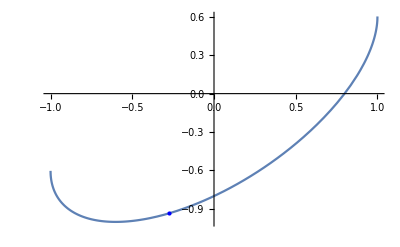

```mathematica
n=40;
Plot[energyi[n],{zi,-1,1},Epilog->{Blue,PointSize@Large,Point[{chain[[Length[chain],n]],energy[n]}]}]
```

Piecewise[{{2.7234 ⅇ^(5 (-0.935387-0.602906 zi+0.8 √(1-zi^2))-5 Abs[-0.276157-zi]), -1<zi<1}, {0, True}}]

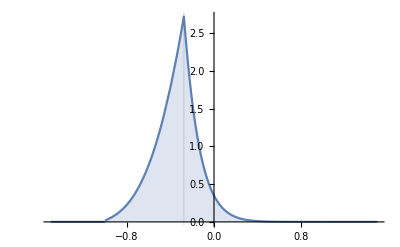

```mathematica
PDF[𝒟[n],zi]
Plot[%,{zi,-1.5,1.5},GridLines->{{{chain[[Length[chain],n]],{Red,Dashed,Thick}}},None},Filling->Axis,PlotRange->All]
```

```mathematica
chain={Table[0,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,250}]
```

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

-Graphics-

```mathematica
last=chain[[Length[chain]]]
```

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

```mathematica
chain[[Length[chain],9]]
```

## Probabilità dallo stato attuale simmetria Z2 two-turns distance

```mathematica
L=180;
hx=0.8;
hz=0.;
δt=5;
δs=5;
chain={Table[0,{i,1,L}]};
chainplus=Table[0,{i,1,L}];
```

```mathematica
chain={{-0.6102201217525546,0.5807184769885196,-0.6161154938350316,0.5337302094209458,-0.5945986980737,0.6153621569073828,-0.5121045825660978,0.3811134527038774,-0.5870882694997746,-0.3230965846393222,-0.5590106394825953,-0.564797911262122,-0.5112132695624015,-0.48455521009750646,-0.6528710012476006,-0.6878021506276948,-0.6292805453868601,-0.5909483280122911,-0.6706765437895488,-0.5989630914430591,-0.537326494381948,-0.6624091865907064,-0.5615191547581165,-0.6581452402256573,-0.4920465057261896,-0.5690768242677207,-0.6842701771350465,-0.4517251952787611,-0.6639909234191496,-0.4990560722938515,-0.6327773890784397,-0.5992270871598405,-0.5714775186489027,-0.48332553852282034,-0.5173629076095057,-0.5449228747715692,-0.44380024569481125,-0.6143141218978455,-0.06631070754057165,-0.5733545169406817,0.14792819738398297,-0.5553339921321732,0.5971761802775842,-0.5650787492417398,0.6625635727248012,-0.4939074021887253,0.6174483682042247,-0.5681109411432083,0.686384543514551,-0.6400473193907982,0.5820180571832055,-0.6703430455071415,0.5803209844665841,-0.62341823552907,0.5981956186747526,-0.5651792575700786,0.5846401814171274,-0.4566898790923736,0.6163891372115659,0.12219607810943912,0.6140260002964998,0.4317331315585751,0.7243096383516381,0.6603168392227042,0.5959195312212818,0.5395179558582243,0.6584054171199759,0.6295934024267488,0.4770181208518432,0.6366027563322556,0.5617837277428694,0.4616882585673058,0.3952728609375946,0.5489051246724546,-0.08539229579423496,0.5382160016989205,-0.40071617578569624,0.6177044599823562,-0.5070704193606527,0.5552922893083068}};
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^(-Abs[z[i]-zi]δs)ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

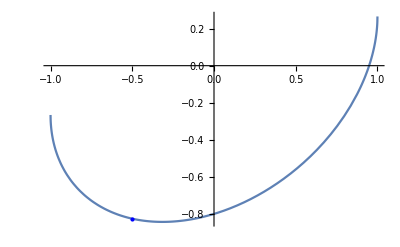

```mathematica
n=39;
Plot[energyi[n],{zi,-1,1},Epilog->{Blue,PointSize@Large,Point[{chain[[Length[chain],n]],energy[n]}]}]
```

Piecewise[{{2.91041 ⅇ^(5 (-0.825742-0.265821 zi+0.8 √(1-zi^2))-5 Abs[-0.499942-zi]), -1<zi<1}, {0, True}}]

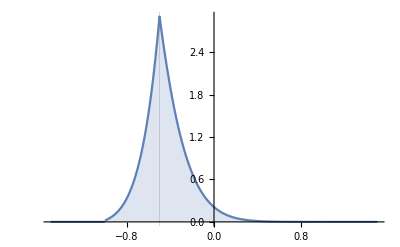

```mathematica
PDF[𝒟[n],zi]
Plot[%,{zi,-1.5,1.5},GridLines->{{{chain[[Length[chain],n]],{Red,Dashed,Thick}}},None},Filling->Axis,PlotRange->All]
```

```mathematica
chain={Table[0,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[If[(EvenQ[Length[chain]]&&EvenQ[i])||(OddQ[Length[chain]]&&OddQ[i]),RandomVariate[𝒟[i]],chain[[Length[chain],i]]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,10}]
```

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

-Graphics-

```mathematica
last=chain[[Length[chain]]]
```

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

```mathematica
chain[[Length[chain],9]]
```

## Probabilità dallo stato attuale simmetria Z2 Mpemba

```mathematica
hxi=0.8;
hzi=0.9;
m=MinValue[{-(0.5 zi zi+0.5 zi zi+hxi √(1-zi^2)+hzi zi),zi≤0,zi≥-1},zi]
```

-0.8

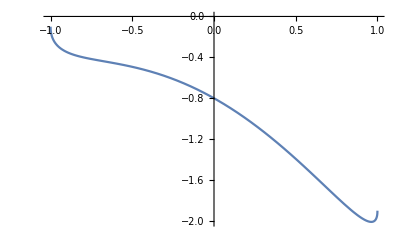

```mathematica
Plot[-(0.5 zi zi+0.5 zi zi+hxi √(1-zi^2)+hzi zi),{zi,-1,1}]
```

```mathematica
L=80;
hx=0.8;
hz=0.02;
δt=30;
chain={Table[m,{i,1,L}]};
chainplus=Table[m,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

-Graphics-

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

Piecewise[{{5.65251 ⅇ^(250 (-0.8+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.448879

```mathematica
chain={Table[m,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,150}]
```

Interpolation::inddp: The point 2.57636×10^-9 in dimension 1 is duplicated.

Interpolation::inddp: The point 3.63913×10^-8 in dimension 1 is duplicated.

Interpolation::inddp: The point -7.23826×10^-8 in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

-Graphics-

```mathematica
0.9
```

-Graphics-

```mathematica
0.8
```

-Graphics-

```mathematica
0.5
```

-Graphics-

```mathematica
0.3
```

-Graphics-

```mathematica
last=chain[[Length[chain]]]
```

{-0.61022,0.580718,-0.616115,0.53373,-0.594599,0.615362,-0.512105,0.381113,-0.587088,-0.323097,-0.559011,-0.564798,-0.511213,-0.484555,-0.652871,-0.687802,-0.629281,-0.590948,-0.670677,-0.598963,-0.537326,-0.662409,-0.561519,-0.658145,-0.492047,-0.569077,-0.68427,-0.451725,-0.663991,-0.499056,-0.632777,-0.599227,-0.571478,-0.483326,-0.517363,-0.544923,-0.4438,-0.614314,-0.0663107,-0.573355,0.147928,-0.555334,0.597176,-0.565079,0.662564,-0.493907,0.617448,-0.568111,0.686385,-0.640047,0.582018,-0.670343,0.580321,-0.623418,0.598196,-0.565179,0.58464,-0.45669,0.616389,0.122196,0.614026,0.431733,0.72431,0.660317,0.59592,0.539518,0.658405,0.629593,0.477018,0.636603,0.561784,0.461688,0.395273,0.548905,-0.0853923,0.538216,-0.400716,0.617704,-0.50707,0.555292}

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

## Probabilità dallo stato attuale simmetria Z2 two-turns Mpemba alternativa

```mathematica
hxi=0.8;
hzi=0.1;
(*m=MinValue[{-(0.5 zi zi+0.5 zi zi+hxi √(1-zi^2)+hzi zi),zi≤0,zi≥-1},zi]*)
```

```mathematica
m=-0.9;
```

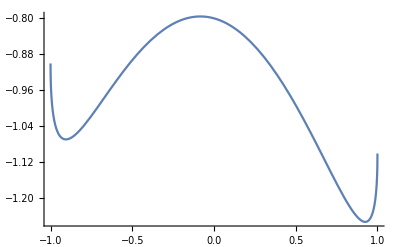

```mathematica
Plot[-(0.5 zi zi+0.5 zi zi+hxi √(1-zi^2)+hzi zi),{zi,-1,1}]
```

```mathematica
L=80;
hx=0.8;
hz=0.02;
δt=30;
chain={Table[m,{i,1,L}]};
chainplus=Table[m,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[1/(1+ⅇ^((energyi[i]-energy[i])δt)),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

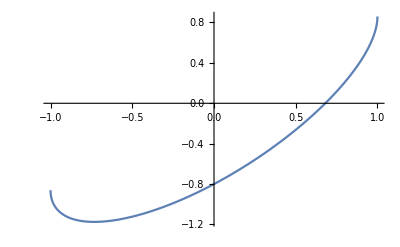

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

Piecewise[{{2.932/(1+ⅇ^(30 (1.14071+0.88 zi-0.8 √(1-zi^2)))), -1<zi<1}, {0, True}}]

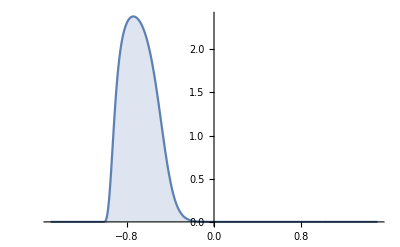

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.448879

```mathematica
chain={Table[m,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[If[(EvenQ[Length[chain]]&&EvenQ[i])||(OddQ[Length[chain]]&&OddQ[i]),RandomVariate[𝒟[i]],chain[[Length[chain],i]]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,250}]
```

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

```mathematica
da 0.a 0.02
```

-Graphics-

```mathematica
da 0.3 a 0.02
```

-Graphics-

```mathematica
da 0.6 a 0.02
```

-Graphics-

```mathematica
da 0.6 a 0.005
```

-Graphics-

```mathematica
da 0.005 a 0.005
```

-Graphics-

```mathematica
0.005 da 0.3
```

-Graphics-

```mathematica
0.01 da 0.3
```

-Graphics-

```mathematica
0.3
```

-Graphics-

```mathematica
0.5
```

-Graphics-

```mathematica
0.7
```

-Graphics-

```mathematica
0.9
```

-Graphics-

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

```mathematica
PDF[𝒟[9],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis]
```

Piecewise[{{0.307083 ⅇ^(15 (-0.731341+0.25075 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

```mathematica
Plot[energyi[34],{zi,-1,1}]
```

-Graphics-

## Probabilità dallo stato attuale alternativa long range

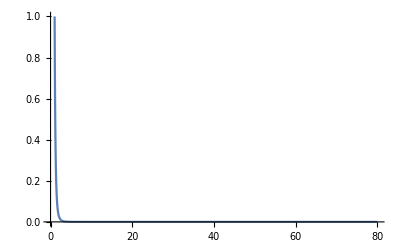

```mathematica
ρ=5;
Plot[1/x^ρ,{x,0,L},PlotRange->{{0,L},{0,1}}]
```

```mathematica
hxi=0.8;
hzi=0.4;
```

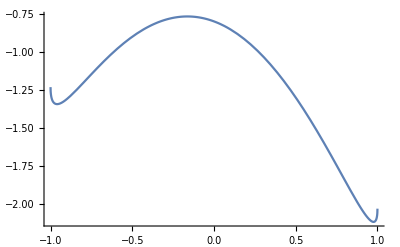

```mathematica
ρ=2;
Plot[-(0.5 Sum[zi/j^ρ ,{j,1,L-1}] zi+0.5 Sum[zi/j^ρ ,{j,1,L-1}] zi+hxi √(1-zi^2)+hzi zi),{zi,-1,1}]
```

```mathematica
m=-0.91;
```

```mathematica
L=80;
hx=0.8;
hz=0.3;
α=2;
δt=40;
chain={Table[m,{i,1,L}]};
chainplus=Table[m,{i,1,L}];
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 Sum[1/j^α z[i-j],{j,1,L-1}]z[i]+0.5Sum[1/j^α z[i+j],{j,1,L-1}]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 Sum[1/j^α z[i-j],{j,1,L-1}]zi+0.5 Sum[1/j^α z[i+j],{j,1,L-1}]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
𝒟[i_]:=ProbabilityDistribution[1/(1+ⅇ^((energyi[i]-energy[i])δt)),{zi,-1,1},Method->"Normalize"];
```

```mathematica
energytot:=Sum[energy[i],{i,1,L}];
```

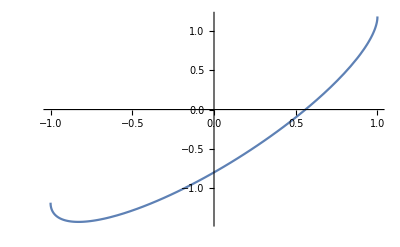

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

Piecewise[{{5.09087/(1+ⅇ^(20 (1.41044+1.18544 zi-0.8 √(1-zi^2)))), -1<zi<1}, {0, True}}]

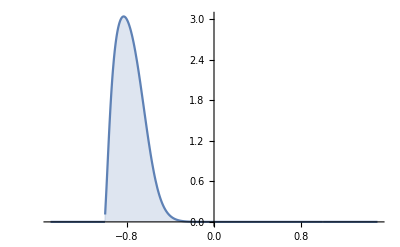

```mathematica
PDF[𝒟[3],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

```mathematica
SeedRandom[]
RandomVariate[𝒟[3]]
```

-0.768749

```mathematica
chain={Table[m,{i,1,L}]};
energ={energytot};
```

```mathematica
SeedRandom[]
Do[
chainplus=Table[RandomVariate[𝒟[i]],{i,1,L}];
chain=Append[chain,chainplus];
energ=Append[energ,energytot],
{i,1,50}]
```

```mathematica
MatrixPlot[Transpose[chain],PlotLegends->Automatic]
```

-Graphics-

```mathematica
30
```

-Graphics-

```mathematica
20
```

-Graphics-

```mathematica
α=5
```

-Graphics-

```mathematica
α=2
```

-Graphics-

```mathematica
α=10
```

-Graphics-

```mathematica
mean=Table[Mean[chain[[i]]],{i,1,Length[chain]}];
ListLinePlot[mean,PlotRange->All]
```

-Graphics-

## Workshop

```mathematica
L=80;
hx=0.8;
hz=0.02;
δt=15;
```

```mathematica
chain={{-0.6102201217525546,0.5807184769885196,-0.6161154938350316,0.5337302094209458,-0.5945986980737,0.6153621569073828,-0.5121045825660978,0.3811134527038774,-0.5870882694997746,-0.3230965846393222,-0.5590106394825953,-0.564797911262122,-0.5112132695624015,-0.48455521009750646,-0.6528710012476006,-0.6878021506276948,-0.6292805453868601,-0.5909483280122911,-0.6706765437895488,-0.5989630914430591,-0.537326494381948,-0.6624091865907064,-0.5615191547581165,-0.6581452402256573,-0.4920465057261896,-0.5690768242677207,-0.6842701771350465,-0.4517251952787611,-0.6639909234191496,-0.4990560722938515,-0.6327773890784397,-0.5992270871598405,-0.5714775186489027,-0.48332553852282034,-0.5173629076095057,-0.5449228747715692,-0.44380024569481125,-0.6143141218978455,-0.06631070754057165,-0.5733545169406817,0.14792819738398297,-0.5553339921321732,0.5971761802775842,-0.5650787492417398,0.6625635727248012,-0.4939074021887253,0.6174483682042247,-0.5681109411432083,0.686384543514551,-0.6400473193907982,0.5820180571832055,-0.6703430455071415,0.5803209844665841,-0.62341823552907,0.5981956186747526,-0.5651792575700786,0.5846401814171274,-0.4566898790923736,0.6163891372115659,0.12219607810943912,0.6140260002964998,0.4317331315585751,0.7243096383516381,0.6603168392227042,0.5959195312212818,0.5395179558582243,0.6584054171199759,0.6295934024267488,0.4770181208518432,0.6366027563322556,0.5617837277428694,0.4616882585673058,0.3952728609375946,0.5489051246724546,-0.08539229579423496,0.5382160016989205,-0.40071617578569624,0.6177044599823562,-0.5070704193606527,0.5552922893083068}};
```

```mathematica
ind[i_]:=If[i>L,i-L,If[i<1,i+L,i]];
z[i_]:=chain[[Length[chain],ind[i]]];
energy[i_]:=-(0.5 z[i-1]z[i]+0.5 z[i+1]z[i]+hx √(1-z[i]^2)+hz z[i]);
energyi[i_]:=-(0.5 z[i-1]zi+0.5 z[i+1]zi+hx √(1-zi^2)+hz zi);
min[i_]:=MinValue[{energyi[i],zi≤1,zi≥-1},zi];
```

```mathematica
𝒟m[i_]:=ProbabilityDistribution[ⅇ^((min[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

```mathematica
𝒟[i_]:=ProbabilityDistribution[ⅇ^((energy[i]-energyi[i])δt),{zi,-1,1},Method->"Normalize"];
```

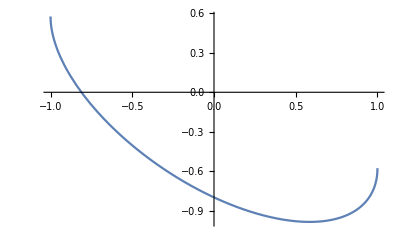

```mathematica
Plot[energyi[3],{zi,-1,1}]
```

Piecewise[{{0.0000446726 ⅇ^(15 (-0.274488+0.577224 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

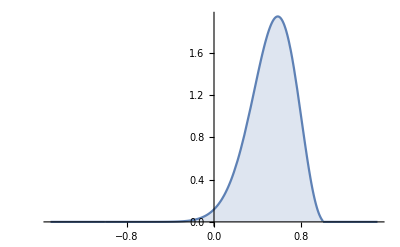

```mathematica
n=3;
PDF[𝒟[n],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

```mathematica
n=3;
PDF[𝒟m[n],zi]
Plot[%,{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```

Piecewise[{{1.94269 ⅇ^(15 (-0.986503+0.577224 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

-Graphics-

Piecewise[{{0.0000446726 ⅇ^(15 (-0.274488+0.577224 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

Piecewise[{{1.94269 ⅇ^(15 (-0.986503+0.577224 zi+0.8 √(1-zi^2))), -1<zi<1}, {0, True}}]

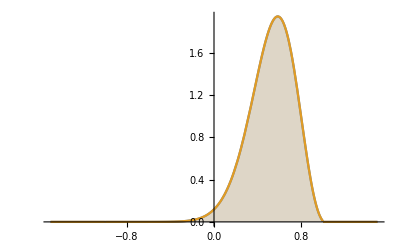

```mathematica
n=3;
f=PDF[𝒟[n],zi]
fm=PDF[𝒟m[n],zi]
Plot[{f,fm},{zi,-1.5,1.5},Filling->Axis,PlotRange->All]
```